## Direct Derivation of the Dynamic Regressor for a Stanford Arm examples of the theoretical results presented in: "Explicit Lagrangian Formulation of the Dynamic Regressors for Serial Manipulators", M. Gabiccini, A. Bracci, D. De Carli, M. Fredianelli, A. Bicchi submitted to the 2009 IEEE International Conference on Robotics and Automation (ICRA2009) to be held in Kobe, Japan, May 12 - 17, 2009

### Package

```mathematica
<<ScrewCalculusPro`ScrewCalculusPro`
<<ToMatlab`ToMatlab`
```

### UR10e Manipulator - definition of required quantities

Denavit-Hartenberg table with joint types added in the last slot [REQUIRED FOR DIRECT REGRESSOR CALCULATION]

```mathematica
tableUR10e[q1_,q2_,q3_,q4_,q5_,q6_]={
{0,            -Pi/2,d1,q1,"R"},
{al2,           0        , d2, q2,"R"},
{al3,            0        ,d3,q3,"R"},
{0,            -Pi/2,d4,q4,"R"},
{0,               Pi/2 ,d5,q5,"R"},
{0,               0         , d6,q6,"R"}
}
```

{{0,-π/2,d1,q1,R},{al2,0,d2,q2,R},{al3,0,d3,q3,R},{0,-π/2,d4,q4,R},{0,π/2,d5,q5,R},{0,0,d6,q6,R}}

Symbolic variable definition [REQUIRED FOR DIRECT REGRESSOR CALCULATION]

```mathematica
qsym={q1,q2,q3,q4,q5,q6}
```

{q1,q2,q3,q4,q5,q6}

List of CGi's position vectors with respect to the local D-H frames [NOT REQUIRED FOR DIRECT REGRESSOR CALCULATION]

```mathematica
CGtableUR10e=Table[ToExpression[{"a"<>ToString[i],"b"<>ToString[i],"c"<>ToString[i]}],{i,1,Length[tableUR10e@@qsym]}]
```

{{a1,b1,c1},{a2,b2,c2},{a3,b3,c3},{a4,b4,c4},{a5,b5,c5},{a6,b6,c6}}

```mathematica
CGtableUR10e ={{0,0,0},{a2,0,0},{a3,0,0},{0,b4,0},{0,b5,0},{0,0,c6}}
```

{{0,0,0},{a2,0,0},{a3,0,0},{0,b4,0},{0,b5,0},{0,0,c6}}

```mathematica
CGtableUR10e ={{0,0,0},
{-0.3060,0,0},
{-0.28615,0,0},
{0,0.1719,0},
{0,-0.1149,0},
{0,0,-0.0922}}
```

{{0,0,0},{-0.306,0,0},{-0.28615,0,0},{0,0.1719,0},{0,-0.1149,0},{0,0,-0.0922}}

List of inertia matrices with respect to the local CGi's [NOT REQUIRED FOR DIRECT REGRESSOR CALCULATION]

```mathematica
tensorlist=Table[ToExpression[{
{"I"<>ToString[i]<>"xx","-I"<>ToString[i]<>"xy","-I"<>ToString[i]<>"xz"},
{"-I"<>ToString[i]<>"xy","I"<>ToString[i]<>"yy","-I"<>ToString[i]<>"yz"},
{"-I"<>ToString[i]<>"xz","-I"<>ToString[i]<>"yz","I"<>ToString[i]<>"zz"}
}],{i,1,Length[tableUR10e@@qsym]}]
```

{{{I1xx,-I1xy,-I1xz},{-I1xy,I1yy,-I1yz},{-I1xz,-I1yz,I1zz}},{{I2xx,-I2xy,-I2xz},{-I2xy,I2yy,-I2yz},{-I2xz,-I2yz,I2zz}},{{I3xx,-I3xy,-I3xz},{-I3xy,I3yy,-I3yz},{-I3xz,-I3yz,I3zz}},{{I4xx,-I4xy,-I4xz},{-I4xy,I4yy,-I4yz},{-I4xz,-I4yz,I4zz}},{{I5xx,-I5xy,-I5xz},{-I5xy,I5yy,-I5yz},{-I5xz,-I5yz,I5zz}},{{I6xx,-I6xy,-I6xz},{-I6xy,I6yy,-I6yz},{-I6xz,-I6yz,I6zz}}}

```mathematica
tensorlist ={{{0.031474312576900,0,0},{0,0.021875625000000,0},{0,0,0.031474312576900}},
{{0.036365625000000,0,0},{0,1.632467283798000,0},{0,0,1.632467283798000}},
{{0.010884375000000,0,0},{0,0.427952347172000,0},{0,0,0.427952347172000}},
{{0.005108247956700,0,0},{0,0.005108247956700,0},{0,0,0.005512500000000}},
{{0.005108247956700,0,0},{0,0.005512500000000,0},{0,0,0.005108247956700}},
{{0.0005264622894150000,0,0},{0,0.0005681250000000000,0},{0,0,0.0005264622894150000}}}
```

{{{0.0314743,0,0},{0,0.0218756,0},{0,0,0.0314743}},{{0.0363656,0,0},{0,1.63247,0},{0,0,1.63247}},{{0.0108844,0,0},{0,0.427952,0},{0,0,0.427952}},{{0.00510825,0,0},{0,0.00510825,0},{0,0,0.0055125}},{{0.00510825,0,0},{0,0.0055125,0},{0,0,0.00510825}},{{0.000526462,0,0},{0,0.000568125,0},{0,0,0.000526462}}}

Extract just the first...

```mathematica
tensorlist[[1]]//MatrixForm
```

(0 | 0 | 0
0 | 0 | 0
0 | 0 | 0)

List of link masses [NOT REQUIRED FOR DIRECT REGRESSOR CALCULATION]

```mathematica
masslist=Table[ToExpression["m"<>ToString[i]],{i,1,Length[tableUR10e@@qsym]}]
```

{m1,m2,m3,m4,m5,m6}

```mathematica
masslist = {7.778,12.93,3.87,1.96,1.96,0.2020}
```

{7.778,12.93,3.87,1.96,1.96,0.202}

```mathematica
r=0.075;
h1=0.178;
h2=1.224;
h3=1.1446;
h4=0.12;
h5=0.12;
h6 = 0.12;
```

```mathematica
tensorlist ={
{{m1/12*(3*r^2+h1^2),0,0},{0,m1/2*(r^2),0},{0,0,m1/12*(3*r^2+h1^2)}},
{{m2/2*(r^2),0,0},{0,m2/12*(3*r^2+h2^2),0},{0,0,m2/12*(3*r^2+h2^2)}},
{{m3/2*(r^2),0,0},{0,m3/12*(3*r^2+h3^2),0},{0,0,m3/12*(3*r^2+h3^2)}},
{{m4/12*(3*r^2+h4^2),0,0},{0,m4/12*(3*r^2+h4^2),0},{0,0,m4/2*(r^2)}},
{{m5/12*(3*r^2+h5^2),0,0},{0,m5/2*(r^2),0},{0,0,m5/12*(3*r^2+h5^2)}},
{{m6/12*(3*r^2+h6^2),0,0},{0,m6/2*(r^2),0},{0,0,m6/12*(3*r^2+h6^2)}}}
```

{{{1/12 m1 (h1^2+3 r^2),0,0},{0,(m1 r^2)/2,0},{0,0,1/12 m1 (h1^2+3 r^2)}},{{(m2 r^2)/2,0,0},{0,1/12 m2 (h2^2+3 r^2),0},{0,0,1/12 m2 (h2^2+3 r^2)}},{{(m3 r^2)/2,0,0},{0,1/12 m3 (h3^2+3 r^2),0},{0,0,1/12 m3 (h3^2+3 r^2)}},{{1/12 m4 (h4^2+3 r^2),0,0},{0,1/12 m4 (h4^2+3 r^2),0},{0,0,(m4 r^2)/2}},{{1/12 m5 (h5^2+3 r^2),0,0},{0,(m5 r^2)/2,0},{0,0,1/12 m5 (h5^2+3 r^2)}},{{1/12 m6 (h6^2+3 r^2),0,0},{0,(m6 r^2)/2,0},{0,0,1/12 m6 (h6^2+3 r^2)}}}

### Time dependent variable definitions [ALL REQUIRED]

Version time dependent, configuration

```mathematica
q[t_]=Map[ToExpression[ToString[#]<>"[t]"]&,qsym]
```

{q1[t],q2[t],q3[t],q4[t],q5[t],q6[t]}

Velocity

```mathematica
qp[t_]=D[q[t],t]
```

{q1'[t],q2'[t],q3'[t],q4'[t],q5'[t],q6'[t]}

Acceleration

```mathematica
qpp[t_]=D[qp[t],t]
```

{q1''[t],q2''[t],q3''[t],q4''[t],q5''[t],q6''[t]}

Reference velocity in the Slotine-Li algorithm

```mathematica
v[t_]=Table[ToExpression["v"<>ToString[i]<>"[t]"],{i,1,Length[tableUR10e@@qsym]}]
```

{v1[t],v2[t],v3[t],v4[t],v5[t],v6[t]}

Its time derivative

```mathematica
vp[t_]=D[v[t],t]
```

{v1'[t],v2'[t],v3'[t],v4'[t],v5'[t],v6'[t]}

Gravity is defined once as

```mathematica
g0={0,0,-g}
```

{0,0,-g}

### Direct regressor calculations

```mathematica
?Regressor
```

Dynamic Regressor for the first link alone

```mathematica
Y1=(Regressor[tableUR10e@@q[t],q[t],qp[t],v[t],vp[t],t,g0,1]//FullSimplify);Y1//MatrixForm
```

(0 | 0 | 0 | 0 | 0 | 0 | 0 | v1'[t] | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0)

{{0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0}}

```mathematica
Y1//Dimensions
```

Dynamic Regressor for the second link alone

```mathematica
Y2=(Regressor[tableUR10e@@q[t],q[t],qp[t],v[t],vp[t],t,g0,2]//FullSimplify);Y2//Simplify//MatrixForm
```

(-al2^2 Cos[q2[t]] Sin[q2[t]] v1[t] q2'[t]+al2 Cos[q2[t]] v2[t] (-al2 Sin[q2[t]] q1'[t]+d2 q2'[t])+(d2^2+al2^2 Cos[q2[t]]^2) v1'[t]+al2 d2 Sin[q2[t]] v2'[t] | d2 Cos[q2[t]] v2[t] q2'[t]-al2 Sin[2 q2[t]] (v2[t] q1'[t]+v1[t] q2'[t])+al2 v1'[t]+al2 Cos[2 q2[t]] v1'[t]+d2 Sin[q2[t]] v2'[t] | -d2 Sin[q2[t]] v2[t] q2'[t]-al2 Cos[2 q2[t]] (v2[t] q1'[t]+v1[t] q2'[t])-al2 Sin[2 q2[t]] v1'[t]+d2 Cos[q2[t]] v2'[t] | al2 Cos[q2[t]] v2[t] q2'[t]+2 d2 v1'[t]+al2 Sin[q2[t]] v2'[t] | Sin[q2[t]] (Cos[q2[t]] (v2[t] q1'[t]+v1[t] q2'[t])+Sin[q2[t]] v1'[t]) | -Cos[2 q2[t]] (v2[t] q1'[t]+v1[t] q2'[t])-Sin[2 q2[t]] v1'[t] | Cos[q2[t]] v2[t] q2'[t]+Sin[q2[t]] v2'[t] | Cos[q2[t]] (-Sin[q2[t]] (v2[t] q1'[t]+v1[t] q2'[t])+Cos[q2[t]] v1'[t]) | -Sin[q2[t]] v2[t] q2'[t]+Cos[q2[t]] v2'[t] | 0
al2 (-g Cos[q2[t]]+Sin[q2[t]] (al2 Cos[q2[t]] v1[t] q1'[t]+d2 v1'[t])+al2 v2'[t]) | -g Cos[q2[t]]+al2 Sin[2 q2[t]] v1[t] q1'[t]+d2 Sin[q2[t]] v1'[t]+2 al2 v2'[t] | g Sin[q2[t]]+al2 Cos[2 q2[t]] v1[t] q1'[t]+d2 Cos[q2[t]] v1'[t] | al2 Sin[q2[t]] v1'[t] | -Cos[q2[t]] Sin[q2[t]] v1[t] q1'[t] | Cos[2 q2[t]] v1[t] q1'[t] | Sin[q2[t]] v1'[t] | Cos[q2[t]] Sin[q2[t]] v1[t] q1'[t] | Cos[q2[t]] v1'[t] | v2'[t]
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0)

Regressor for the whole manipulator

```mathematica
Y=(Regressor[tableUR10e@@q[t],q[t],qp[t],v[t],vp[t],t,g0]);
```

```mathematica
Y=Y /.
```

```mathematica
Y//Dimensions
```

{6,60}

Structure of the Regressor for the Stanford Manipulator - the white columns show which parameters do not affect the manipulator dynamics

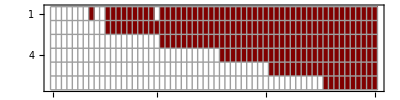

```mathematica
MatrixPlot[Y,ColorFunction->"Monochrome",AspectRatio->(1/4),Mesh-> All]
```

```mathematica
theFile=File["Yyyyy.txt"];
Export[theFile,Y//Chop];
```

### Standard way of deriving the equations of motion

Calculation of all 6 equations of motion

```mathematica
classicaleqs=DynamicEquations[tableUR10e@@q[t],CGtableUR10e,masslist,tensorlist,g0,q[t],qp[t],v[t],vp[t]];
```

We show just the first one...

```mathematica
classicaleqs[[1]]
```

0.+11+(0.+3+(-Cos[q5[t]] Sin[q1[t]]+(Cos[q4[t]] (Cos[q1[t]] Cos[q2[t]] Cos[q3[t]]-Cos[q1[t]] Sin[q2[t]] Sin[q3[t]])+(-Cos[q1[t]] Cos[q3[t]] Sin[q2[t]]-Cos[q1[t]] Cos[q2[t]] Sin[q3[t]]) Sin[q4[t]]) Sin[q5[t]]) (0.000526462 (1) Sin[q5[t]] (-Cos[q5[t]] Sin[q1[t]]+(Cos[q4[t]] (Cos[q1[t]] Cos[q2[t]] Cos[q3[t]]-Cos[q1[t]] Sin[q2[t]] Sin[q3[t]])+(-Cos[q1[t]] Cos[q3[t]] Sin[q2[t]]-Cos[q1[t]] Cos[q2[t]] Sin[q3[t]]) Sin[q4[t]]) Sin[q5[t]])+1+0.000568125 (1) (Cos[q6[t]] (Cos[q4[t]] (1)-1)-(1) 1))) 1
 |  |  |  |

```mathematica
theFile=File["tau.txt"];
Export[theFile,classicaleqs//Chop];
```

### Equations of motion obtained multiplying the Dynamic Regressor and the List of Dynamic Parameters

Contestualmente alla creazione della lista di parametri (10 per ciascun link) i momenti di inerzia vengono scritti rispetto all'origine del frame di DH ancora in componenti nel frame di DH.

As we create the complete list with masses, first moments of inertia and second moments of inertia, we calculate the moments of inertia with respect to the local D-H frames, as indicated in the paper

```mathematica
paramlist=ExtractParameters[CGtableUR10e,masslist,tensorlist]//Simplify;paramlist
```

{m1,0,0,0,I1xx,0,0,I1yy,0,I1zz,m2,a2 m2,0,0,I2xx,0,0,I2yy+a2^2 m2,0,I2zz+a2^2 m2,m3,a3 m3,0,0,I3xx,0,0,I3yy+a3^2 m3,0,I3zz+a3^2 m3,m4,0,b4 m4,0,I4xx+b4^2 m4,0,0,I4yy,0,I4zz+b4^2 m4,m5,0,b5 m5,0,I5xx+b5^2 m5,0,0,I5yy,0,I5zz+b5^2 m5,m6,0,0,c6 m6,I6xx+c6^2 m6,0,0,I6yy+c6^2 m6,0,I6zz}

Extract just the parameters for the first link...

```mathematica
paramlist[[1;;10]]
```

{m1,0,0,0,I1xx,0,0,I1yy,0,I1zz}

Equations of motion with the regressor

```mathematica
regressoreqs=Y.paramlist;
```

### A little detour inside the package (just to show other useful functions)

Computation of the forward kinematics for the defined Denavit-Hartenberg table

```mathematica
FK= DHFKine[tableUR10e@@qsym]//FullSimplify
FK//Dimensions
```

{{Cos[q6] Sin[q1] Sin[q5]+Cos[q1] (Cos[q2+q3+q4] Cos[q5] Cos[q6]-Sin[q2+q3+q4] Sin[q6]),-Sin[q1] Sin[q5] Sin[q6]-Cos[q1] (Cos[q6] Sin[q2+q3+q4]+Cos[q2+q3+q4] Cos[q5] Sin[q6]),-Cos[q5] Sin[q1]+Cos[q1] Cos[q2+q3+q4] Sin[q5],-(d2+d3+d4+d6 Cos[q5]) Sin[q1]+Cos[q1] (al2 Cos[q2]+al3 Cos[q2+q3]-d5 Sin[q2+q3+q4]+d6 Cos[q2+q3+q4] Sin[q5])},{Cos[q2+q3+q4] Cos[q5] Cos[q6] Sin[q1]-Cos[q1] Cos[q6] Sin[q5]-Sin[q1] Sin[q2+q3+q4] Sin[q6],-Cos[q6] Sin[q1] Sin[q2+q3+q4]+(-Cos[q2+q3+q4] Cos[q5] Sin[q1]+Cos[q1] Sin[q5]) Sin[q6],Cos[q1] Cos[q5]+Cos[q2+q3+q4] Sin[q1] Sin[q5],Cos[q1] (d2+d3+d4+d6 Cos[q5])+Sin[q1] (al2 Cos[q2]+al3 Cos[q2+q3]-d5 Sin[q2+q3+q4]+d6 Cos[q2+q3+q4] Sin[q5])},{-Cos[q5] Cos[q6] Sin[q2+q3+q4]-Cos[q2+q3+q4] Sin[q6],-Cos[q2+q3+q4] Cos[q6]+Cos[q5] Sin[q2+q3+q4] Sin[q6],-Sin[q2+q3+q4] Sin[q5],d1-d5 Cos[q2+q3+q4]-al2 Sin[q2]-al3 Sin[q2+q3]-d6 Sin[q2+q3+q4] Sin[q5]},{0,0,0,1}}

{4,4}

```mathematica
theFile=File["FK.txt"];
```

```mathematica
Export[theFile,FK];
```

Full Jacobian (classical for differntial kinematics)

```mathematica
JJ=DHJacob0[tableUR10e@@qsym]//FullSimplify
```

```mathematica
theFile=File["JJ.txt"];
Export[theFile,JJ];
```

```mathematica
D[JJ[q1_,q2_,q3_,q4_,q5_,q6_]=DHJacob0[tableUR10e@@q[t]]//FullSimplify,t]//FullSimplify
```

Derivata del jacobiano

```mathematica
theFile=File["DJJ.txt"];
Export[theFile,D[JJ[q1_,q2_,q3_,q4_,q5_,q6_]=DHJacob0[tableUR10e@@q[t]]//FullSimplify,t]//FullSimplify];
```

Set::write: Tag List in «1» is Protected.

Partial Jacobians (version for regressor dynamics) - reference points are still the origins of DH frames

For the first link

```mathematica
DHJacob0Dyn[tableUR10e@@qsym,1]//FullSimplify
```

For the second link

```mathematica
DHJacob0Dyn[tableUR10e@@qsym,2]//FullSimplify
```

Partial Jacobians (version for classical dynamics) - reference points are now the CGs of the link - a separate list must be supplied

First link

```mathematica
CGJacob0Dyn[tableUR10e@@qsym,CGtableUR10e,1]
```

Third link

```mathematica
CGJacob0Dyn[tableUR10e@@qsym,CGtableUR10e,3]
```

Inertia matrix

```mathematica
Bmat[q1_,q2_,q3_,q4_,q5_,q6_]=Inertia[tableUR10e@@qsym,CGtableUR10e,masslist,tensorlist]//Simplify
```

```mathematica
f=OpenWrite["B_regzz.m"]
```

```mathematica
WriteMatlab[Bmat[q1_,q2_,q3_,q4_,q5_,q6_]=Inertia[tableUR10e@@qsym,CGtableUR10e,masslist,tensorlist]//Simplify,f,"B",200]
```

```mathematica
Close[f]
```

B_regzz.m

```mathematica
theFile=File["B_reg.txt"];
Export[theFile,Bmat[q1_,q2_,q3_,q4_,q5_,q6_]=Inertia[tableUR10e@@qsym,CGtableUR10e,masslist,tensorlist]//Simplify];
```

We map it of the time dependent joint vector

```mathematica
Bmat@@qsym
```

We check its symmetry!

```mathematica
Bmat@@qsym
```

```mathematica
(*Bmat@@qsym-Transpose[Bmat@@qsym]//Simplify*)
```

We compute the Coriolis matrix derived from the Christoffel symbols

```mathematica
Cmat=InertiaToCoriolis[Bmat@@q[t],q[t],qp[t]];
```

```mathematica
Cmat[1]
```

```mathematica
Cmat = Simplify[Cmat,TimeConstraint->0.1]//Timing
```

```mathematica
Cmat=Cmat//Chop;
```

```mathematica
Cmat = Cmat//Simplify;
```

$Aborted

```mathematica
theFile=File["C_reg.txt"];
Export[theFile,Cmat//Simplify];
```

```mathematica
fsf=OpenWrite["C_regzbbbz.m"]
```

```mathematica
WriteMatlab[Cmat,fsf,"C",200];
```

```mathematica
Close[fsf]
```

C_regzbbbz.m

```mathematica
Gvec=Gravitational[tableUR10e@@qsym,CGtableUR10e,masslist,g0]//Simplify
```

{0,-1/2 g (2 (a2 m2+al2 (m2+m3+m4+m5+m6)) Cos[q2]+2 (a3 m3+al3 (m3+m4+m5+m6)) Cos[q2+q3]-2 b5 m5 Sin[q2+q3+q4]-2 d5 m5 Sin[q2+q3+q4]-2 d5 m6 Sin[q2+q3+q4]-c6 m6 Sin[q2+q3+q4-q5]-d6 m6 Sin[q2+q3+q4-q5]+c6 m6 Sin[q2+q3+q4+q5]+d6 m6 Sin[q2+q3+q4+q5]),g (-(a3 m3+al3 (m3+m4+m5+m6)) Cos[q2+q3]+(b5 m5+d5 (m5+m6)) Sin[q2+q3+q4]-(c6+d6) m6 Cos[q2+q3+q4] Sin[q5]),g (b5 m5+d5 (m5+m6)) Sin[q2+q3+q4]-(c6+d6) g m6 Cos[q2+q3+q4] Sin[q5],-(c6+d6) g m6 Cos[q5] Sin[q2+q3+q4],0}

```mathematica
Gvec/.g->1/.a2->1
```

```mathematica
theFile=File["G_reg.txt"];
Export[theFile,Gvec];
```

```mathematica
Gvec[[6]]//Simplify
```

0.

```mathematica
tau =(Bmat@@q[t])*qpp[t]+Cmat*qp[t]+Gvec;
```

```mathematica
theFile=File["tauuu.txt"];
Export[theFile,tau];
```

```mathematica
tau = tau//Simplify
```